## Pre-Computing the BRDF Integral

We need to find a way to approximate the lighting integral for the specular part of our area light.
The integral writes as:

	L(ω_o)=∫_Ω L(ω_i) f_r(ω_o,ω_i)(ω_i.n)dω_i
	
Ω is the solid angle covered by the upper hemisphere above the surface.

We proceed in the same way as http://blog.selfshadow.com/publications/s2013-shading-course/karis/s2013_pbs_epic _notes _v2.pdf to separate the integral in several parts:

#### Splitting the integral

L(ω_o)≃ ∫_Ω L(ω_i,ρ) (ω_i.n) dω_i  ∫_Ω f_r(ω_o,ω_i)(ω_i.n)dω_i

∫_Ω L'(ω_i,ρ) (ω_i.n) dω_i  represents the pre-filtered source of radiance. It could be an env-map in the case of IBL, or our area light in this case.
∫_Ω f_r(ω_o,ω_i)(ω_i.n)dω_i represents the BRDF integral as if lit by a uniform source of radiance (L(ω_i)=1).

#### BRDF integral

Here, we’ re going to concentrate on the BRDF integral.
Assuming the BRDF f_r(ω_o,ω_i) is our Ward-Dür model, coupled with Fresnel, we obtain:

	L_brdf(ω_o)≃ ∫_Ω  F(ω_o,ω_i,n) D(ω_o,ω_i,n) (ω_i.n)dω_i

F(ω_o,ω_i,n) is the Fresnel term (note that we’ll use the Schlick' s fresnel approximation, not our complex fresnel otherwise the integral would be more difficult to separate).
D(ω_o,ω_i,n) is the Normal Distribution Function of the micro-facet model.
There is no masking/shadowing term as it is already accounted for by the Ward-Dür NDF.

Assuming the Schlick fresnel term is:

	F_schlick(ω_o,h)=F_0+(1-F_0)(1-ω_o.h)^5 = F_0 (1-(1-ω_o.h)^5) + (1-ω_o.h)^5 

We can further split the integral into 2 parts:

	L_brdf(ω_o)≃ F_0∫_Ω  (1-(1-ω_o.h)^5)D(ω_o,ω_i,n) (ω_i.n)dω_i + ∫_Ω  (1-ω_o.h)^5 D(ω_o,ω_i,n) (ω_i.n)dω_i

Ignoring anisotropy, we have:

	D(ω_o,ω_i,n,α) = ρ_s/πα^2 e^(-(tan^2 Θ_h)/α^2) 2(1+cos Θ_l cos Θ_v +sin Θ_l sin Θ_v cos( Φ_v-Φ_l))/(cos Θ_l + cos Θ_v)^4 

Or:
	D(ω_o,ω_i,n,α) = ρ_s/πα^2 e^(-(tan^2 Θ_h)/α^2) (ĥ.ĥ)/(ĥ.n)^4
	
and ĥ = ω_o +ω_i  (non-normalized!)
	
This gives us:

	L_brdf(ω_o,α)≃ ρ_s/πα^2[ F_0∫_Ω  (1-(1-ω_o.h)^5)e^(-(tan^2 Θ_h)/α^2) (ĥ.ĥ)/(ĥ.n)^4 (ω_i.n)dω_i + ∫_Ω  (1-ω_o.h)^5 e^(-(tan^2 Θ_h)/α^2) (ĥ.ĥ)/(ĥ.n)^4 (ω_i.n)dω_i]
	
	L_brdf(ω_o.n,α)≃ ρ_s/2[F_0 A(ω_o.n,α) +B(ω_o.n,α)]

Where:
	A(ω_o.n,α)= 1/α^2∫_0^(π/2)  (1-(1-ω_o.n)^5)e^(-(tan^2 Θ_h)/α^2)(ĥ.ĥ)/(ĥ.n)^4 sin Θ dΘ
	B(ω_o.n,α) = 1/α^2∫_0^(π/2)  (1-ω_o.n)^5 e^(-(tan^2 Θ_h)/α^2) (ĥ.ĥ)/(ĥ.n)^4 sin Θ dΘ

Both A and B are bounded in [0,1] because the integral of BRDF is ≤ 1, as shown by Dür in his paper.

#### WRONG! Light direction is NOT the reflected view direction! Now, in our special case, we also have the incoming (light) direction ω_i which is the reflection of the outgoing (view) direction: ω_i= 2(ω_o.n).n - ω_o or simply, in terms of angles, Θ_l=Θ_v and Φ_l=Φ_v+π h = (ω_i+ω_o)/(|ω_i+ω_o|)=(2(ω_o.n).n)/(2(ω_o.n))=n So D(ω_o,ω_i,n) further simplifies into: D(ω_o,ω_i,n) = ρ_s/πα^2 e^(-((tan Θ_h)/α^2)^2) 2(1+cos Θ_l cos Θ_v +sin Θ_l sin Θ_v cos( Φ_v-Φ_l))/(cos Θ_l + cos Θ_v)^4 = ρ_s/πα^2 2(1+cos^2 Θ_v -sin^2 Θ_v )/(2 cos Θ_v)^4=ρ_s/πα^2(4 cos^2 Θ_v)/(16 cos^4 Θ_v)=ρ_s/(4 πα^2 cos^2 Θ_v) And L_brdf(ω_o) becomes: L_brdf(ω_o.n,α)≃ ρ_s/(4π)[F_0∫_Ω (1-(1-ω_o.n)^5)1/(α^2(ω_o.n))dω_i +∫_Ω (1-ω_o.n)^5 1/(α^2(ω_o.n))dω_i] L_brdf(ω_o.n,α)≃ ρ_s/2[F_0∫_0^(π/2) (1-(1-ω_o.n)^5)1/(α^2(ω_o.n))sin Θ dΘ +∫_0^(π/2) (1-ω_o.n)^5 1/(α^2(ω_o.n))sin Θ dΘ] L_brdf(ω_o.n,α)≃ ρ_s/2[F_0 A(ω_o.n,α) +B(ω_o.n,α)] Where: A(ω_o.n,α)= ∫_0^(π/2) (1-(1-ω_o.n)^5)1/(α^2(ω_o.n))sin Θ dΘ B(ω_o.n,α) = ∫_0^(π/2) (1-ω_o.n)^5 1/(α^2(ω_o.n))sin Θ dΘ

### Plotting the 2 parts

```mathematica
SetDirectory[NotebookDirectory[]]; 
rawBRDFpart = BinaryReadList["./BRDF0_64x64.bin",{"Real32", "Real32"}]
```

{{0.00031577,0.995778},{0.0757202,0.924233},{0.146784,0.853202},{0.213407,0.786586},{0.275803,0.724193},4086,{0.491529,0.000150126},{0.489565,0.000114701},{0.48753,0.0000850902},{0.485661,0.0000613634},{0.483747,0.000041618}}
 |  |  |  |

```mathematica
BRDFpartA = Table[rawBRDFpart[[x+64*(y-1)]][[1]], {x,1,64},{y,1,64}];
BRDFpartB = Table[rawBRDFpart[[x+64*(y-1)]][[2]], {x,1,64},{y,1,64}];
ListPlot3D[BRDFpartA]
ListPlot3D[BRDFpartB,PlotRange->Full]
```

-Graphics3D-

-Graphics3D-

```mathematica
Integrate[Cos[θ]Sin[θ],θ]
```

-1/2 Cos[θ]^2

### Examining the Beckmann distribution

```mathematica
beckman[a_,m_]:= Exp[-(Tan[a]/m)^2] / (4*Pi*m^2);
Manipulate[ { Plot[beckman[a,m], {a,0.0,π/2},PlotRange->Full], beckman[0,m]},{m,1/100,π/2}]
```

```mathematica
Integrate[beckman[a,0.1],{a,0,∞}]
```

∫_0^∞ 7.95775 ⅇ^(-100. Tan[a]^2)ⅆa

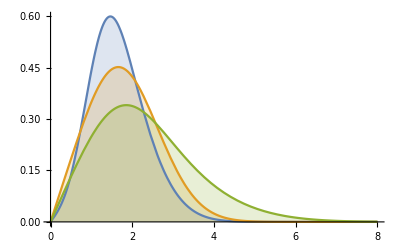

```mathematica
Plot[Evaluate@Table[PDF[BeckmannDistribution[1,-1,1,σ2],x],{σ2,{1/2,1,2}}],{x,0,8},Filling->Axis]
```

## Visualizing shadowing term G_Schlick(L,V,H)

Assuming L⃗ is the reflection of V⃗ by the plane of normal N⃗ we can write L⃗ = -V⃗+ 2(N⃗.V⃗).N⃗
G_Schlick(v) = (n.v)/((n.v)(1-k) + k) where k=(m+1)^2/8 and m the materials roughness.

```mathematica
Gschlick[x_,k_]:= x/(x*(1-k)+k)
```

```mathematica
Manipulate[Plot[Gschlick[Cos[x],(m+1)^2/8]^2,{x,0,π/2}], {{m,0.01},0,1}]
```

## Paraboloïd Shadow Mapping

```mathematica
Plot3D[{1-x^2-y^2,0},{x,-1,1},{y,-1,1}]
```

-Graphics3D-

### Using a sigmoïd to simulate the step function

```mathematica
sigmoid[x_,k_] := 1 / (1+Exp[-k*x]);
Manipulate[Plot[sigmoid[x,k], {x,-10, 10},PlotRange->Full], {{k,1},1/100,100}]
```

```mathematica
Series[sigmoid[x,10],{x,0,8}]
```

1/2+(5 x)/2-(125 x^3)/6+(625 x^5)/3-(265625 x^7)/126+O[x]^9

```mathematica
approx[x_]:=1/2+(5 x)/2-(125 x^3)/6+(625 x^5)/3-(265625 x^7)/126
```

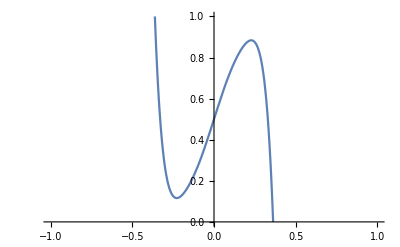

```mathematica
Plot[approx[x],{x,-1,1},PlotRange->{0,1}]
```

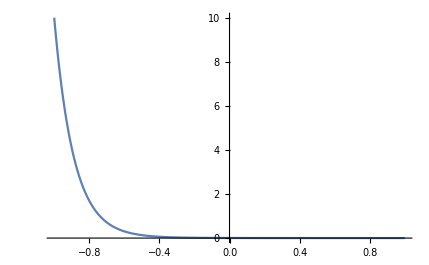

```mathematica
a = 1.0;
b =  0.1;
altitude = 100.0;
hitDistance = 100.0;
density[dy_]:= a  Exp[-b * altitude] (1 - Exp[-b * dy * hitDistance]) / (b * dy);
Plot[density[x], {x, -1.0, 1 }, PlotRange->Full]
```